```mathematica
ClearAll["`*"]
Subscript[f, 0]=220;
Subscript[t, 0]=1/Subscript[f, 0];
SetOptions[{FourierCoefficient,FourierCosCoefficient,FourierSinCoefficient},FourierParameters :>{1,2π/Subscript[t, 0]}];
```

```mathematica
x[t_]:=Abs[Sin[2*Pi*Subscript[f, 0]*t]];
Subscript[x, ak][k_]:= FourierCoefficient[x[t],t,k]
Subscript[x, fourier][t_,k_]:= FourierSeries[x[t],t,k]
```

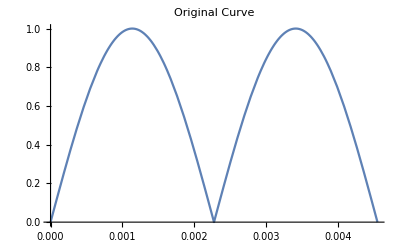

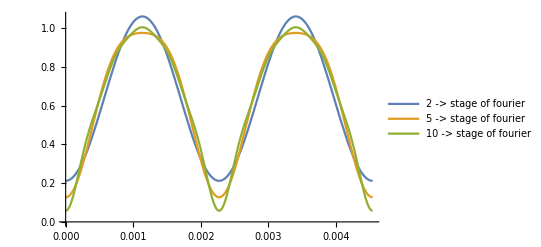

```mathematica
Plot[x[t],{t,0,Subscript[t, 0]},PlotLabel->"Original Curve"]
Plot[{Evaluate[Subscript[x, fourier][t,2]],Evaluate[Subscript[x, fourier][t,5]],Evaluate[Subscript[x, fourier][t,10]]},{t,0,Subscript[t, 0]},PlotLegends->{"2 -> stage of fourier" ,"5 -> stage of fourier","10 -> stage of fourier","20 -> stage of fourier"}]
```

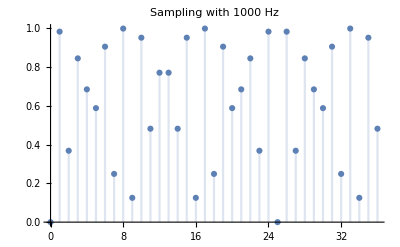

```mathematica
DiscretePlot[x[k/1000],{k,0,36},PlotLabel->"Sampling with 1000 Hz"]
```

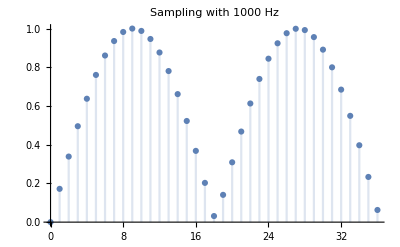

```mathematica
DiscretePlot[x[k/8000],{k,0,36},PlotLabel->"Sampling with 1000 Hz"]
```

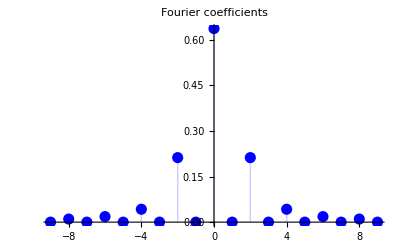

```mathematica
DiscretePlot[
Abs[Subscript[x, ak][k]],{k,-9,9},
PlotRange->All,PlotStyle->Directive[PointSize[0.02],Thick,Blue],
PlotLabel->"Fourier coefficients"
]
```

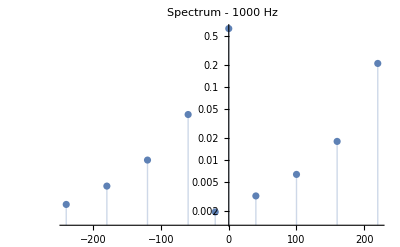

```mathematica
spectrum8=Flatten[Table[{(k Subscript[f, 0]+1000m )/2,Subscript[x, ak][k]}/.Solve[Abs[k Subscript[f, 0]+1000m]≤1000/2,m,Integers],{k,0,18,2}],1];
ListLogPlot[Function[fa,{fa⟦1⟧,Abs[fa⟦2⟧]}]/@spectrum8,PlotLabel->"Spectrum - 1000 Hz",Filling->Axis]
```

```mathematica
spectrum8=Flatten[Table[{(k Subscript[f, 0]+8000m )/2,Subscript[c, n][k]}/.Solve[Abs[k Subscript[f, 0]+8000m]≤8000/2,m,Integers],{k,0,18,2}],1]
ListLogPlot[Function[fa,{fa⟦1⟧,Abs[fa⟦2⟧]}]/@spectrum8,PlotLabel->"Spectrum - Sampling w/ 8000 Hz",Filling->Axis]
```

{{0,c_n[0]},{220,c_n[2]},{440,c_n[4]},{660,c_n[6]},{880,c_n[8]},{1100,c_n[10]},{1320,c_n[12]},{1540,c_n[14]},{1760,c_n[16]},{1980,c_n[18]}}

-Graphics-

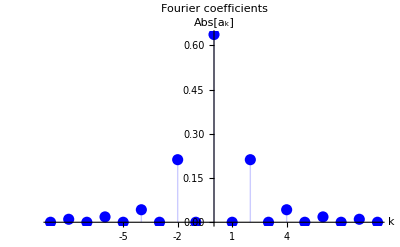

```mathematica
DiscretePlot[
Abs[Subscript[x, ak][k]],{k,-9,9},
PlotRange->All,PlotStyle->Directive[PointSize[0.02],Thick,Blue],
AxesLabel->{HoldForm[k],HoldForm[Abs[Subscript[a, k]]]},Ticks->{Range[-5,5],Automatic},PlotLabel->"Fourier coefficients"
]
```

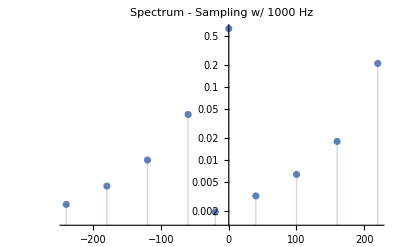

```mathematica
spectrum=Flatten[Table[{(k Subscript[f, 0]+1000m )/2,Subscript[x, ak][k]}/.Solve[Abs[k Subscript[f, 0]+1000m]≤1000/2,m,Integers],{k,0,18,2}],1];
ListLogPlot[Function[fa,{fa⟦1⟧,Abs[fa⟦2⟧]}]/@spectrum,PlotLabel->"Spectrum - Sampling w/ 1000 Hz",Filling->Axis]
```

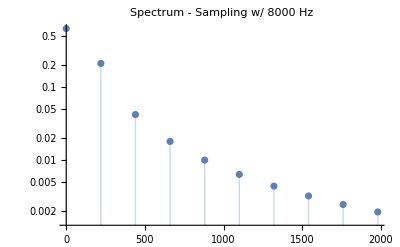

```mathematica
spectrum=Flatten[Table[{(k Subscript[f, 0]+8000m )/2,Subscript[x, ak][k]}/.Solve[Abs[k Subscript[f, 0]+8000m]≤8000/2,m,Integers],{k,0,18,2}],1];
ListLogPlot[Function[fa,{fa⟦1⟧,Abs[fa⟦2⟧]}]/@spectrum,PlotLabel->"Spectrum - Sampling w/ 8000 Hz",Filling->Axis]
```